## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PSCVT";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
pathMASSef = "C:/MASSef/";
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit_PSCVT_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:C:\MASSef\Enzyme\PSCVT\

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

(pep^c+skm5p^c⇌(3psme)^c+pi^c)^PSCVT

ordered bi bi;

Structure: 1

Active sites: 1

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pep | Null
skm5p | Null | 172 | 163.4
180.6 | Null | Null | 7 | Null | Null | Null
1 | pep | Null
skm5p | Null | 695 | 660.25
729.75 | Null | Null | 5.5 | Null | Null | Null
1 | pep | Null
skm5p | Null | 193 | 183.35
202.65 | Null | Null | 6.8 | Null | Null | Null
1 | pep | Null
skm5p | Null | 147 | 139.65
154.35 | Null | Null | 7.5 | Null | Null | Null
1 | pep | Null
skm5p | Null | 141 | 133.95
148.05 | Null | Null | 7.8 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pep | 0.000015 | 0.00001425
0.00001575 | skm3P | 200 uM | M | 7 | 25 |  | 
1 | skm5p | 3.5×10^-6 | 3.325×10^-6
3.675×10^-6 | pep | 500 uM | M | 7 | 25 |  | 
1 | pi | 0.0025 | 0.002375
0.002625 | 3psme | 50 uM | M | 7 | 25 |  | 
1 | pep | 0.000016 | 0.0000152
0.0000168 | skm3P | 200 uM | M | 7 | 25 |  | 
1 | skm5p | 2.5×10^-6 | 2.375×10^-6
2.625×10^-6 | pep | 200 uM | M | 7 | 25 |  | 
1 | 3psme | 3.×10^-6 | 2.85×10^-6
3.15×10^-6 | pi | 50 mM | M | 7 | 25 |  | 
1 | pi | 0.0025 | 0.002375
0.002625 | 3psme | 50 uM | M | 7 | 25 |  | 
1 | skm5p | 3.6×10^-6 | 3.4×10^-6
3.8×10^-6 |  | M | 7 | 30 |  | 
1 | skm5p | 3.2×10^-6 | 3.×10^-6
3.4×10^-6 |  | M | 7 | 30 |  | 
1 | pep | 0.000023 | 0.000021
0.000025 |  | M | 7 | 30 |  | 
1 | pep | 0.000021 | 0.00002
0.000022 |  | M | 7 | 30 |  | 
1 | skm5p | 0.000018 | 0.000014
0.000022 |  | M | 7.5 | 25 |  | k | 50 mM
cl | 50 mM
1 | pep | 0.00004 | 0.000031
0.000049 |  | M | 7.5 | 25 |  | k | 50 mM
cl | 50 mM
1 | skm5p | 0.00011 | 0.00009
0.00013 |  | M | 7.5 | 25 |  | k | 100 mM
cl | 100 mM
1 | pep | 0.00015 | 0.00012
0.00018 |  | M | 7.5 | 25 |  | k | 100 mM
cl | 100 mM
1 | skm5p | 0.00014 | 0.00012
0.00016 |  | M | 7.5 | 25 |  | k | 100 mM
cl | 100 mM
1 | pep | 0.00016 | 0.00014
0.00018 |  | M | 7.5 | 25 |  | k | 100 mM
cl | 100 mM
1 | pep | 0.000045 | 0.00004
0.00005 |  | M | 7.5 |  |  | 
1 | skm5p | 0.000048 | 0.000043
0.000053 |  | M | 7.5 |  |  | 
1 | pi | 0.0046 | 0.0032
0.006 | 3psme | 50 uM | M | 7 | 25 |  | 
1 | 3psme | 0.000011 | 9.×10^-6
0.000013 | pi | 50 mM | M | 7 | 25 |  | 
1 | pep | 0.0001 | 0.000074
0.000126 | skm3P | 200 uM | M | 7 | 25 |  | 
1 | skm5p | 0.000135 | 0.000085
0.000185 | pep | 200 uM | M | 7 | 25 |  | 
1 | pep | 0.0000223 | 0.00001604
0.00002856 |  | M | 7 | 30 |  | 
1 | pep | 0.000025 | 0.00002375
0.00002625 |  | M | 7 | 25 |  | 
1 | skm5p | 0.00002 | 0.000019
0.000021 |  | M | 7 | 25 |  | 
1 | pep | 0.000088 | 0.0000836
0.0000924 |  | M | 6.8 | 20 |  | 
1 | skm5p | 0.00012 | 0.000114
0.000126 |  | M | 6.8 | 20 |  | 
1 | pep | 0.0001 | 0.000095
0.000105 |  | M | 7.8 | 25 |  | 
1 | pep | 0.0225 | 0.01618
0.02882 |  | M | 7 | 30 |  | 
1 | pep | 0.00002 | 0.000019
0.000021 |  | M | 7.8 | 25 |  | 
1 | skm5p | 8.×10^-6 | 4.×10^-6
0.000012 |  | M | 7 | 25 |  | 
1 | pep | 0.000013 | 9.×10^-6
0.000017 |  | M | 7 | 25 |  | 
1 | pi | 0.005 | 0.003
0.007 |  | M | 7 | 25 |  | 
1 | 3psme | 0.00001 | 5.×10^-6
0.000015 |  | M | 7 | 25 |  | 
1 | pep | 0.0001 | 0.000096
0.000104 |  | M | 5.5 |  |  | 
1 | skm5p | 0.00009 | 0.000085
0.000095 |  | M | 5.5 |  |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pep | Null
skm5p | Null | 107.492 | 106.542
108.441 | 1/s | 7 | 37 |  | 
1 | pep | Null
skm5p | Null | 107.681 | 106.162
109.201 | 1/s | 7 | 37 |  | 
1 | pep | Null
skm5p | Null | 96.09 | 93.0871
99.0928 | 1/s | 7.5 | 37 |  | k | 50 mM
cl | 50 mM
1 | pep | Null
skm5p | Null | 39.0365 | 36.0337
42.0394 | 1/s | 7.5 | 37 |  | k | 100 mM
cl | 100 mM
1 | pep | Null
skm5p | Null | 42.0394 | 39.0365
45.0422 | 1/s | 7.5 | 37 |  | k | 100 mM
cl | 100 mM
1 | pep | Null | 41.9 2.5^(0.1 (37-)) | 39.805 2.5^(0.1 (37-))
43.995 2.5^(0.1 (37-)) | 1/s | 7.5 | 37 |  | 
1 | skm5p | Null | 43.7 2.5^(0.1 (37-)) | 41.515 2.5^(0.1 (37-))
45.885 2.5^(0.1 (37-)) | 1/s | 7.5 | 37 |  | 
1 | pep | Null | 125.344 | 119.076
131.611 | 1/s | 6.8 | 37 |  | 
1 | skm5p | Null | 136.738 | 129.901
143.575 | 1/s | 6.8 | 37 |  | 
1 | pep | Null
skm5p | Null | 79.2742 | 75.3105
83.2379 | 1/s | 7.8 | 37 |  | 
1 | pep | Null | 45. 2.5^(0.1 (37-)) | 43.2 2.5^(0.1 (37-))
46.8 2.5^(0.1 (37-)) | 1/s | 5.5 | 37 |  | 
1 | skm5p | Null | 40.5 2.5^(0.1 (37-)) | 38.25 2.5^(0.1 (37-))
42.75 2.5^(0.1 (37-)) | 1/s | 5.5 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {0,0,0,1,0};
kmPriorities = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
s05Priorities = Null;
kcatPriorities = {0,0,0,0,1,0,0,0,0,0,0,0};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(pep^c+skm5p^c⇌(3psme)^c+pi^c)^PSCVT

ordered bi bi;

Structure: 1

Active sites: 1

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pep | Null
skm5p | Null | 147 | 139.65
154.35 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | skm5p | 0.00014 | 0.00012
0.00016 |  | M | 7.5 | 25 |  | k | 100 mM
cl | 100 mM
1 | pep | 0.00016 | 0.00014
0.00018 |  | M | 7.5 | 25 |  | k | 100 mM
cl | 100 mM

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pep | Null
skm5p | Null | 42.0394 | 39.0365
45.0422 | 1/s | 7.5 | 37 |  | k | 100 mM
cl | 100 mM

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_PSCVT[c] + skm5p[c] <=> E_PSCVT[c]&skm5p",
				"E_PSCVT[c]&skm5p + pep[c] <=> E_PSCVT[c]&skm5p&pep",
				"E_PSCVT[c]&skm5p&pep <=> E_PSCVT[c]&3psme&pi",
				"E_PSCVT[c]&3psme&pi <=> E_PSCVT[c]&3psme + pi[c]",
                                               "E_PSCVT[c]&3psme <=> E_PSCVT[c] + 3psme[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PSCVT^c)_^+skm5p^c⇌(PSCVT^c&skm5p^c)_^)^PSCVT1,((PSCVT^c&(3psme)^c)_^⇌(PSCVT^c)_^+(3psme)^c)^PSCVT2,((PSCVT^c&skm5p^c)_^+pep^c⇌(PSCVT^c&skm5p^c&pep^c)_^)^PSCVT3,((PSCVT^c&(3psme)^c&pi^c)_^⇌(PSCVT^c&(3psme)^c)_^+pi^c)^PSCVT4,((PSCVT^c&skm5p^c&pep^c)_^⇌(PSCVT^c&(3psme)^c&pi^c)_^)^PSCVT5}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PSCVT^c)_^+skm5p^c⇌(PSCVT^c&skm5p^c)_^)^PSCVT1,Overscript[(PSCVT^c&(3psme)^c)_^⇌(PSCVT^c)_^+(3psme)^c, PSCVT2],((PSCVT^c&skm5p^c)_^+pep^c⇌(PSCVT^c&skm5p^c&pep^c)_^)^PSCVT3,Overscript[(PSCVT^c&(3psme)^c&pi^c)_^⇌(PSCVT^c&(3psme)^c)_^+pi^c, PSCVT4],((PSCVT^c&skm5p^c&pep^c)_^⇌(PSCVT^c&(3psme)^c&pi^c)_^)^PSCVT5};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((PSCVT^c&skm5p^c&pep^c)_^-((PSCVT^c&(3psme)^c&pi^c)_^)/K_PSCVT5) Volume_c k_PSCVT5^⟶}

Volume_c (-(PSCVT^c&(3psme)^c&pi^c)_^ k_PSCVT5^⟵+(PSCVT^c&skm5p^c&pep^c)_^ k_PSCVT5^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	3psme[c]	pep[c]	pi[c]	skm5p[c]	param_PSCVT_total	param_pH	param_Temp	FileFlag	Target_Data

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	10
filesWithFunctions	[C:\MASSef\Enzyme\PSCVT\fit_PSCVT_typeII\input\absRateFor.txt, C:\MASSef\Enzyme\PSCVT\fit_PSCVT_typeII\input\absRateRev.txt, C:\MASSef\Enzyme\PSCVT\fit_PSCVT_typeII\input\relRateFor_pep.txt, C:\MASSef\Enzyme\PSCVT\fit_PSCVT_typeII\input\relRateFor_skm5p.txt, C:\MASSef\Enzyme\PSCVT\fit_PSCVT_typeII\input\relRateRev_3psme.txt, C:\MASSef\Enzyme\PSCVT\fit_PSCVT_typeII\input\relRateRev_pi.txt, C:\MASSef\Enzyme\PSCVT\fit_PSCVT_typeII\input\haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	10
filesWithFunctions	[C:\MASSef\Enzyme\PSCVT\fit_PSCVT_typeII\input\absRateFor.txt, C:\MASSef\Enzyme\PSCVT\fit_PSCVT_typeII\input\absRateRev.txt, C:\MASSef\Enzyme\PSCVT\fit_PSCVT_typeII\input\relRateFor_pep.txt, C:\MASSef\Enzyme\PSCVT\fit_PSCVT_typeII\input\relRateFor_skm5p.txt, C:\MASSef\Enzyme\PSCVT\fit_PSCVT_typeII\input\relRateRev_3psme.txt, C:\MASSef\Enzyme\PSCVT\fit_PSCVT_typeII\input\relRateRev_pi.txt, C:\MASSef\Enzyme\PSCVT\fit_PSCVT_typeII\input\haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 0.837269243809
best_fit: 0.919520423393
best_fit: 1.017445236
best_fit: 0.933030926086
best_fit: 1.03764503177

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 4.18243×10^-11 | 1.74927×10^-21 | 1.41565×10^-8 | 9.63024×10^-9 | 147 | 147.
1 | haldaneRatio_1 | 4.18243×10^-11 | 1.74927×10^-21 | 1.41565×10^-8 | 9.63024×10^-9 | 147 | 147.
1 | haldaneRatio_1 | 4.18243×10^-11 | 1.74927×10^-21 | 1.41565×10^-8 | 9.63024×10^-9 | 147 | 147.
1 | haldaneRatio_1 | 4.18243×10^-11 | 1.74927×10^-21 | 1.41565×10^-8 | 9.63024×10^-9 | 147 | 147.
1 | haldaneRatio_1 | 4.18243×10^-11 | 1.74927×10^-21 | 1.41565×10^-8 | 9.63024×10^-9 | 147 | 147.
1 | haldaneRatio_1 | 4.18243×10^-11 | 1.74927×10^-21 | 1.41565×10^-8 | 9.63024×10^-9 | 147 | 147.
1 | haldaneRatio_1 | 4.18243×10^-11 | 1.74927×10^-21 | 1.41565×10^-8 | 9.63024×10^-9 | 147 | 147.
1 | haldaneRatio_1 | 4.18243×10^-11 | 1.74927×10^-21 | 1.41565×10^-8 | 9.63024×10^-9 | 147 | 147.
1 | haldaneRatio_1 | 4.18243×10^-11 | 1.74927×10^-21 | 1.41565×10^-8 | 9.63024×10^-9 | 147 | 147.
1 | haldaneRatio_1 | 4.18243×10^-11 | 1.74927×10^-21 | 1.41565×10^-8 | 9.63024×10^-9 | 147 | 147.
1 | haldaneRatio_1 | 4.18243×10^-11 | 1.74927×10^-21 | 1.41565×10^-8 | 9.63024×10^-9 | 147 | 147.
1 | relRateFor_skm5p | 0.0000225707 | 5.09438×10^-10 | 4.72452×10^-6 | 0.00519697 | 0.0909091 | 0.0909044
1 | relRateFor_skm5p | 0.0000183614 | 3.37142×10^-10 | 5.78391×10^-6 | 0.00422779 | 0.136807 | 0.136801
1 | relRateFor_skm5p | 0.0000124962 | 1.56155×10^-10 | 5.7765×10^-6 | 0.00287732 | 0.20076 | 0.200754
1 | relRateFor_skm5p | 4.79352×10^-6 | 2.29778×10^-11 | 3.14287×10^-6 | 0.00110374 | 0.284747 | 0.284744
1 | relRateFor_skm5p | 4.572×10^-6 | 2.09032×10^-11 | 4.07269×10^-6 | 0.00105275 | 0.386863 | 0.386867
1 | relRateFor_skm5p | 0.0000149485 | 2.23459×10^-10 | 0.0000172104 | 0.00344209 | 0.5 | 0.500017
1 | relRateFor_skm5p | 0.0000253253 | 6.41371×10^-10 | 0.0000357553 | 0.00583154 | 0.613137 | 0.613173
1 | relRateFor_skm5p | 0.0000346915 | 1.2035×10^-9 | 0.0000571367 | 0.00798833 | 0.715253 | 0.71531
1 | relRateFor_skm5p | 0.000042395 | 1.79734×10^-9 | 0.0000780241 | 0.00976229 | 0.79924 | 0.799318
1 | relRateFor_skm5p | 0.0000482611 | 2.32913×10^-9 | 0.0000959278 | 0.0111131 | 0.863193 | 0.863289
1 | relRateFor_skm5p | 0.000052471 | 2.75321×10^-9 | 0.000109842 | 0.0120826 | 0.909091 | 0.909201
1 | relRateFor_pep | 0.0000258012 | 6.657×10^-10 | 5.40069×10^-6 | 0.00594076 | 0.0909091 | 0.0909037
1 | relRateFor_pep | 0.0000209902 | 4.40589×10^-10 | 6.61196×10^-6 | 0.00483306 | 0.136807 | 0.1368
1 | relRateFor_pep | 0.0000142867 | 2.04109×10^-10 | 6.60414×10^-6 | 0.00328957 | 0.20076 | 0.200753
1 | relRateFor_pep | 5.48297×10^-6 | 3.0063×10^-11 | 3.59491×10^-6 | 0.00126249 | 0.284747 | 0.284744
1 | relRateFor_pep | 5.22124×10^-6 | 2.72614×10^-11 | 4.65104×10^-6 | 0.00120224 | 0.386863 | 0.386868
1 | relRateFor_pep | 0.000017081 | 2.91761×10^-10 | 0.0000196656 | 0.00393313 | 0.5 | 0.50002
1 | relRateFor_pep | 0.0000289411 | 8.37589×10^-10 | 0.0000408604 | 0.00666416 | 0.613137 | 0.613178
1 | relRateFor_pep | 0.0000396462 | 1.57182×10^-9 | 0.0000652975 | 0.00912929 | 0.715253 | 0.715318
1 | relRateFor_pep | 0.000048451 | 2.3475×10^-9 | 0.0000891702 | 0.0111569 | 0.79924 | 0.799329
1 | relRateFor_pep | 0.0000551556 | 3.04214×10^-9 | 0.000109633 | 0.0127009 | 0.863193 | 0.863303
1 | relRateFor_pep | 0.0000599674 | 3.59609×10^-9 | 0.000125536 | 0.013809 | 0.909091 | 0.909216
1 | absRateFor | 3.31826×10^-9 | 1.10109×10^-17 | 3.21205×10^-7 | 7.64058×10^-7 | 42.0394 | 42.0394
1 | absRateFor | 3.31826×10^-9 | 1.10109×10^-17 | 3.21205×10^-7 | 7.64058×10^-7 | 42.0394 | 42.0394
1 | absRateFor | 3.31826×10^-9 | 1.10109×10^-17 | 3.21205×10^-7 | 7.64058×10^-7 | 42.0394 | 42.0394
1 | absRateFor | 3.31826×10^-9 | 1.10109×10^-17 | 3.21205×10^-7 | 7.64058×10^-7 | 42.0394 | 42.0394
1 | absRateFor | 3.31826×10^-9 | 1.10109×10^-17 | 3.21205×10^-7 | 7.64058×10^-7 | 42.0394 | 42.0394
1 | absRateFor | 3.31826×10^-9 | 1.10109×10^-17 | 3.21205×10^-7 | 7.64058×10^-7 | 42.0394 | 42.0394
1 | absRateFor | 3.31826×10^-9 | 1.10109×10^-17 | 3.21205×10^-7 | 7.64058×10^-7 | 42.0394 | 42.0394
1 | absRateFor | 3.31826×10^-9 | 1.10109×10^-17 | 3.21205×10^-7 | 7.64058×10^-7 | 42.0394 | 42.0394
1 | absRateFor | 3.31826×10^-9 | 1.10109×10^-17 | 3.21205×10^-7 | 7.64058×10^-7 | 42.0394 | 42.0394
1 | absRateFor | 3.31826×10^-9 | 1.10109×10^-17 | 3.21205×10^-7 | 7.64058×10^-7 | 42.0394 | 42.0394
1 | absRateFor | 3.31826×10^-9 | 1.10109×10^-17 | 3.21205×10^-7 | 7.64058×10^-7 | 42.0394 | 42.0394

### Simulated Data and Best Fit Data Plot

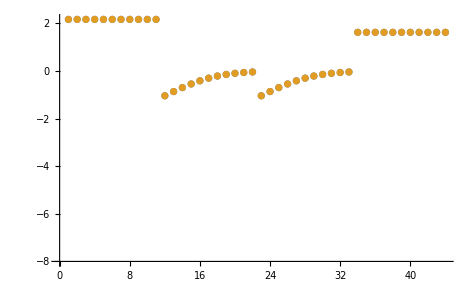

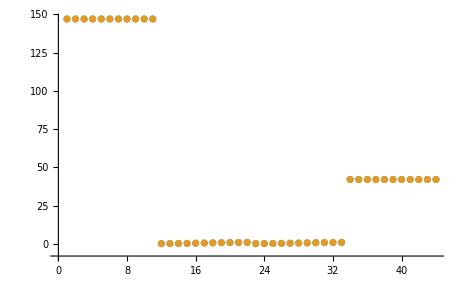

```mathematica
dataSetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

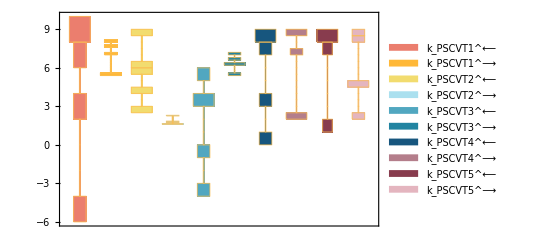

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

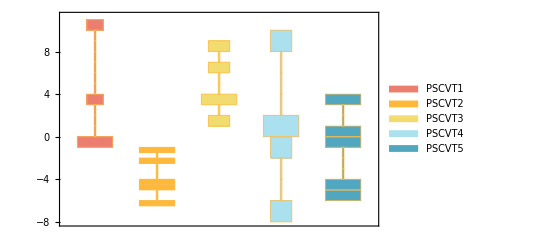

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

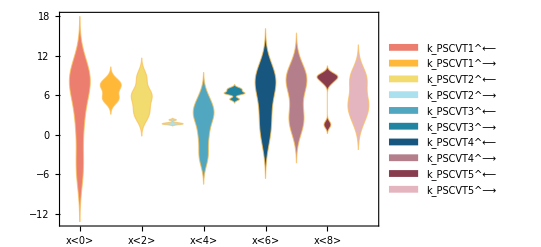

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

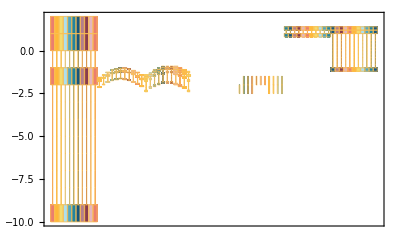

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

data value | predicted value | error in %
0.000045 | 0.000044999 | 0.00221261
0.00089 | 0.00088961 | 0.0437745
0.00053 | 0.000529862 | 0.0260555

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
1059.36 | 1059.36 | 0.0000114381

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.452 | 0.452 | 2.37024×10^-7

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.452 | 0.452 | 2.37024×10^-7

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

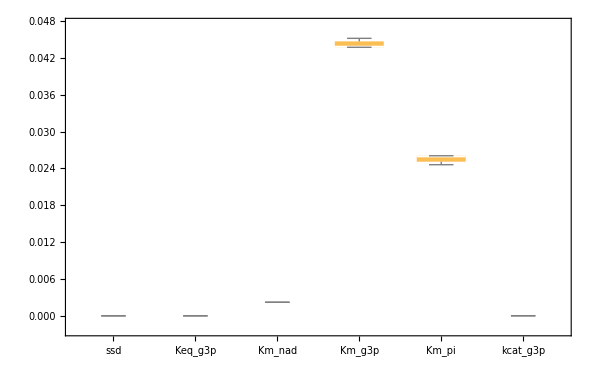

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```